```mathematica
(* create a cobweb plot of f *)
cobweb[f_,{xMin_,xMax_},x0_:{0.2},n_:1000,OptionsPattern[]]:=
Module[{p1,p2,cob,points,allPoints={}},

p1=Plot[{f[x],x}, {x, xMin, xMax},
PlotStyle->Gray,ImageSize->Large,AxesLabel->{x,y}];

For[i=1,i≤Length[x0],i++,
cob=NestList[f,x0[[i]],n];
points=Partition[Riffle[cob,cob],2,1];
points[[1,2]]=0;
AppendTo[allPoints,points];
];

p2=Graphics[{Thickness[0.002],Red,Opacity[1],Line[allPoints]}];

Show[p1,p2,Options[cobweb]]
   ];
```

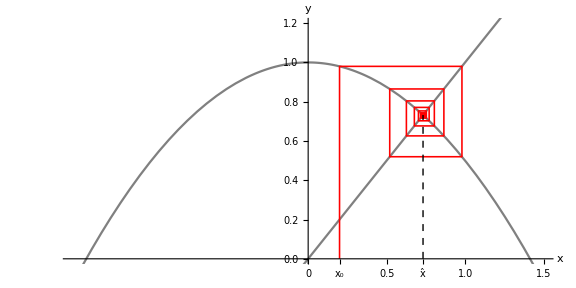

```mathematica
mu=0.5;
f=1-mu*#1^2&;
xHat=(Sqrt[4*mu+1]-1)/(2*mu);
x0=0.2;
xticks=(Charting`FindTicks[{0,1},{0,1}]@@{0,2})~Join~{{xHat,OverHat[x]},{x0,"x_0"}};
Options[cobweb]={PlotRange->{{-1.5,1.5},{0,1.2}},Ticks->{xticks,Automatic},AspectRatio->1/2,
Epilog->{Directive[{Dashed,Black}],Line[{{xHat,0},{xHat,f[xHat]}}]},BaseStyle->{ScriptMinSize->3}};
cobweb[f,{-1.5,1.5},{x0}]
```

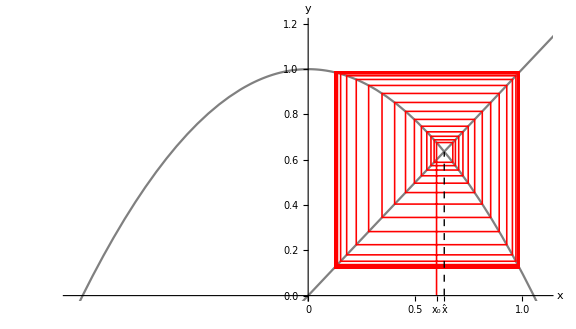

```mathematica
mu=0.9;
f=1-mu*#1^2&;
xHat=(Sqrt[4*mu+1]-1)/(2*mu);
x0=0.6;
xticks=(Charting`FindTicks[{0,1},{0,1}]@@{0,2})~Join~{{xHat,OverHat[x]},{x0,Subscript["x",0]}};
Options[cobweb]={PlotRange->{{-1.1,1.1},{0,1.2}},Ticks->{xticks,Automatic},AspectRatio->1/1.75,
Epilog->{Directive[{Dashed,Black}],Line[{{xHat,0},{xHat,f[xHat]}}]},BaseStyle->{ScriptMinSize->3}};
cobweb[f,{-1.2,1.2},{x0}]
```

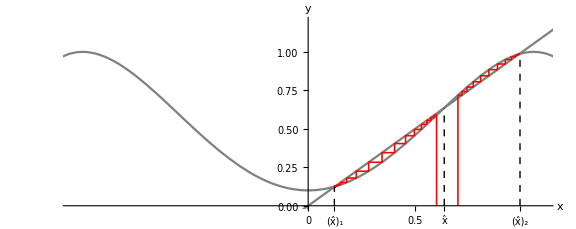

```mathematica
mu=0.9;
f=1-mu*#1^2&;
xHat=(Sqrt[4*mu+1]-1)/(2*mu);
xHat1=0.1225;
xHat2=0.99;
xticks=(Drop[Charting`FindTicks[{0,1},{0,1}]@@{0,2},{3,3}])~Join~{{xHat,OverHat[x]},{xHat1,Subscript[OverHat[x],1]},{xHat2,Subscript[OverHat[x],2]}};
Options[cobweb]={PlotRange->{{-1.1,1.1},{0,1.2}},Ticks->{xticks,Automatic},AspectRatio->1/2.5,Epilog->{Directive[{Dashed,Black}],Line[{{xHat,0},{xHat,f[xHat]}}],Line[{{xHat1,0},{xHat1,f2[xHat1]}}],Line[{{xHat2,0},{xHat2,f2[xHat2]}}]},BaseStyle->{ScriptMinSize->3}};
f2[x_]:=Nest[f,x,2];
cobweb[f2,{-1.2,1.2},{0.6,0.7}]
```

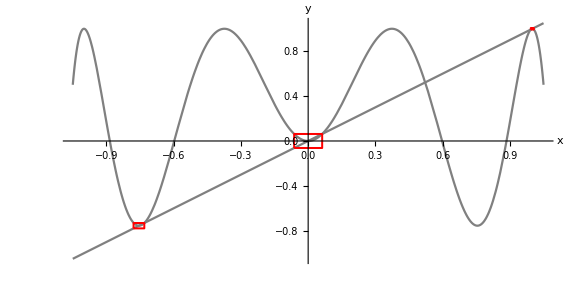

```mathematica
Clear[mu];
labelAnimator={u_,u1_,u2_,opts___}:>{u,u1,u2,Labeled[Animator[Dynamic[u],{u1,u2},opts],Pane[Dynamic[u],{50,Automatic}],Right]&};
Options[cobweb]={PlotRange->{{-1.5,1.5},{-1.2,1.2}}};
g[r_,x_]:=1-r*x^2;
g3[r_,x_]:=g[r,g[r,g[r,x]]];
r=mu/.N[Solve[g3[mu,0]==0,mu,Reals]][[1]];
x=y/.Solve[g3[r,y]==y,y];
f3[x_]:=g3[r,x];
Plot[{y,g3[r,y]},{y,-1.05,1.05},PlotStyle->Gray,ImageSize->Large,AxesLabel->{"x","y"},AspectRatio->1/2,
Epilog->{EdgeForm[{Thickness[0.0025],Red}],FaceForm[],
Rectangle[{-x[[5]],-f3[x[[5]]]},{x[[5]],f3[x[[5]]]}],
Rectangle[{x[[7]],f3[x[[7]]]},{2*x[[8]]-x[[7]],2*f3[x[[8]]]-f3[x[[7]]]}],
Rectangle[{2*x[[2]]-x[[3]],2*f3[x[[2]]]-f3[x[[3]]]},{x[[3]],f3[x[[3]]]}]}]
```

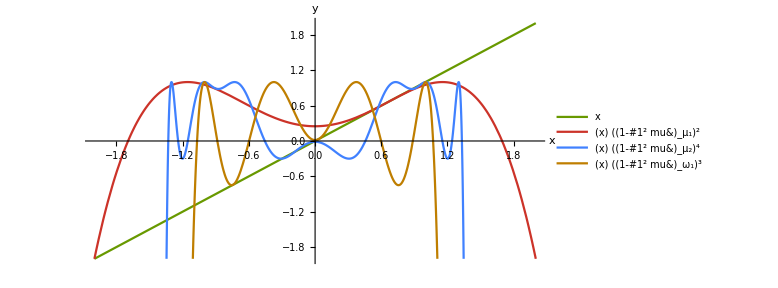

```mathematica
Plot[{y,g[0.75,g[0.75,y]],g[1.3,g3[1.3,y]],g3[1.75,y]},{y,-2,2},
ImageSize->Large,AxesLabel->{"x","y"},PlotStyle->ColorData[90],AspectRatio->1/2,PlotRange->{{-2,2},{-2,2}},
PlotLegends->Placed[{"x","(x)"Subscript[f, Subscript[μ, 1]]^2,"(x)"Subscript[f, Subscript[μ, 2]]^4,"(x)"Subscript[f, Subscript[ω, 1]]^3},{0.945,0.16}]]
```